# Advanced Analysis

Once simulation data has been loaded into Mathematica as DataTable or DataRegion objects, the full power of Mathematica can be used.  The data can remain in discrete form, for example as a DataRegion, or it can be interpolated to provide a continuous function.  In the latter case, it can be used with functions like NDSolve, NIntegrate, FindRoot etc.  We now give some examples of more sophisticated data analysis that can be performed with simulation data.

## Line Integral

The first example is to integrate the grid function phi along the line joining the two black holes in the example data.  (This has no physical significance; it’s just a demonstration.)

Load the data:

```mathematica
phi=ReadGridFunction[$SimulationToolsTestSimulation,"phi","xy",RefinementLevel->3,Iteration->6144]
```

DataRegion[ML_BSSN::phi.01.01,<43,83>,{{-0.75,9.75},{-10.25,10.25}}]

Plot the data:

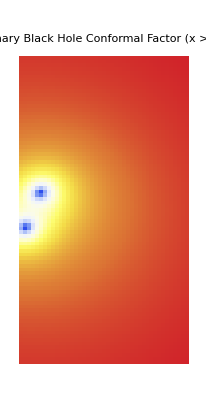

```mathematica
arrayPlot=ArrayPlot[phi,
ColorFunction->ColorData[{"TemperatureMap",{0,1}}],
FrameTicks->True,
FrameLabel->{"xCell[""]","y"},
PlotLabel->"Binary Black Hole Conformal Factor (x > 0)"]
```

Construct a 2-dimensional interpolating function from the data:

```mathematica
phiFn=Interpolation[phi]
```

InterpolatingFunction[{{-0.75,9.75},{-10.25,10.25}},<>]

The coordinate time of this data:

```mathematica
t0=GetTime[phi]
```

96.

The coordinate positions of the black holes at this time:

```mathematica
x1=Interpolation[#][t0]&/@ReadBinaryCoordinates[$SimulationToolsTestSimulation,1]
```

{0.442727,1.16551,-4.98722×10^-20}

```mathematica
x2=Interpolation[#][t0]&/@ReadBinaryCoordinates[$SimulationToolsTestSimulation,2]
```

{-0.442727,-1.16551,-4.98722×10^-20}

The line joining the two can be expressed in parametric form

```mathematica
bhLine=Take[x1+(x2-x1)t,2]
```

{0.442727-0.885453 t,1.16551-2.33102 t}

and used in ParametricPlot.  Mathematica plots can be combined using Show:

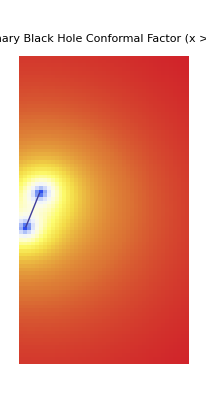

```mathematica
Show[arrayPlot,
ParametricPlot[bhLine,{t,0,1}]]
```

We can now plot phi along this line:

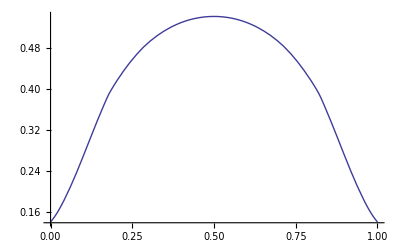

```mathematica
Plot[phiFn@@bhLine,{t,0,1}]
```

Note that the @@ (Apply) is needed because the InterpolatingFunction phiFn takes two separate coordinate arguments, whereas bhLine is a list containing the two coordinates.

Finally, we can compute the integral along the line:

```mathematica
dRdt=Norm[D[bhLine,t]]
```

2.49353

```mathematica
NIntegrate[phiFn@@bhLine dRdt,{t,0,1}]
```

1.02234

## Surface Integral

We can compute surface integrals in a similar way.  First load a 3D data set:

```mathematica
phi3D=phi=ReadGridFunction[$SimulationToolsTestSimulation,"phi","xyz",RefinementLevel->3,Iteration->0]
```

DataRegion[ML_BSSN::phi.01.01,<52,73,40>,{{-0.75,12.},{-9.,9.},{-0.75,9.}}]

```mathematica
Dimensions[phi3D]
```

{52,73,40}

Find the initial position of the first black hole:

```mathematica
x0=Map[Interpolation[#][0]&,ReadBinaryCoordinates[$SimulationToolsTestSimulation,1]]
```

{3.,0.,0.}

Interpolate the 3D data:

```mathematica
phi3DFn=Interpolation[phi3D]
```

InterpolatingFunction[{{-0.75,12.},{-9.,9.},{-0.75,9.}},<>]

Choose a surface of radius 2 centred on the black hole:

```mathematica
R=2;
```

Plot phi as a function of θ and ϕ:

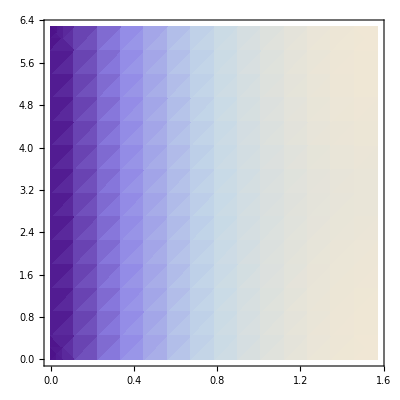

```mathematica
DensityPlot[phi3DFn@@({R  Sin[th]Cos[ph],R Sin[th]Sin[ph],R Cos[th]}+x0 )R Sin[th],
{th,0,Pi/2},{ph,0,2Pi},PlotRange->All]
```

Compute the surface integral:

```mathematica
NIntegrate[
phi3DFn@@({R Sin[th]Cos[ph],R Sin[th]Sin[ph],R Cos[th]}+x0 )R Sin[th],
{th,0,Pi/2},{ph,0,2Pi}]
```

Less::nord: Invalid comparison with 0.  - 0.494933\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

9.2842

(The warnings are a result of the poor convergence of the numerical integral on discretely-sampled data)